# Ionization wave

## Cartoon

## image sequence

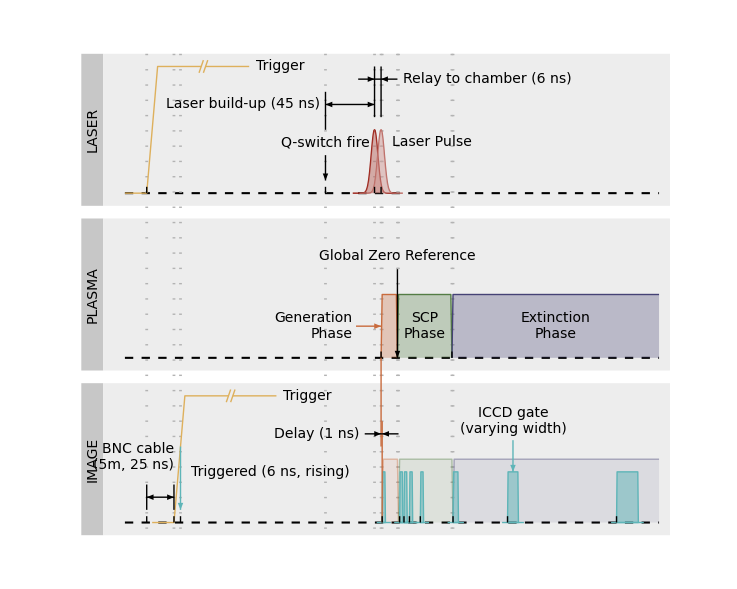

```mathematica
(*--text annotation--*)
opt={FontFamily->"Arial",FontColor->Black,FontSize->14,FontWeight->Plain};

(* -- laser pulse -- *)
a=3/Log[2];
f[t_]:=5Exp[-(t/a)^2];
laser[x_,y_,col_]:={
{col,AbsoluteThickness[1],Line[Table[{x+t,y+f[t]},{t,-20,20,.05}]]},
{EdgeForm[Transparent],FaceForm[{Lighter@col,Opacity[.5]}],Polygon[Table[{x+t,y+f[t]},{t,-20,20,.05}]]}
};

(* -- trigger -- *)
trigger[x_,y_]:={
RGBColor[.87,.69,.36,1],AbsoluteThickness[1],
Line[{{x-20,y},{x,y},{x+10,y+10},{x+50,y+10}}],
Line[{{x+54,y+10},{x+94,y+10}}],
Line[{{x+48,y+10-.5},{x+52,y+10+.5}}],
Line[{{x+52,y+10-.5},{x+56,y+10+.5}}],
Text[Style["Trigger",FontColor->RGBColor[.87,.69,.36,1],opt],{x+100,y+10},{-1,0}]
};

(* -- ICCD gate -- *)
gate[x_,y_,w_]:={
{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1],Line[{{x-5,y},{x+w+5,y}}]},
{EdgeForm[{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1]}],FaceForm[{RGBColor[0.37, 0.71, 0.72, 1],Opacity[.5]}],Polygon[{{x,y},{x+.5,y+4},{x+w-.5,y+4},{x+w,y}}]}
};

(* -- grids & ticks -- *)
grids=Table[
{RGBColor[.7,.7,.7,1],AbsoluteThickness[2],AbsoluteDashing[{1,10}],Line[{{t,11},{t,-27}}]},
{t,{-230,-205,-199,-66,-21,-15,-14,0,1,50,51}}];
ticks[x_List,y_]:=Table[{Black,AbsoluteThickness[1],Line[{{t,y},{t,y+.5}}]},{t,x}];

(* -- plot -- *)
gf=ListLinePlot[

{},

Prolog->{
(* -- laser -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-1},{-270,11}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-1},{250,11}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,0},{240,0}}]},
Text[Style["LASER",FontWeight->Bold,opt],{-280,5},{0,0},{0,1}],

(* -- plasma -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-14},{-270,-2}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-14},{250,-2}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,-13},{240,-13}}]},
Text[Style["PLASMA",FontWeight->Bold,opt],{-280,-8},{0,0},{0,1}],

(* -- Image -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-27},{-270,-15}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-27},{250,-15}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,-26},{240,-26}}]},
Text[Style["IMAGE",FontWeight->Bold,opt],{-280,-21},{0,0},{0,1}],

(* -- vertical grids -- *)
grids
},

Epilog->{
(* -- laser -- *)
trigger[-230,0],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-66,3},{-66,1}}]},
Text[Style["Q-switch fire",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-66,4},{0,0}],
Text[Style["Laser Pulse",FontColor->RGBColor[0.6, 0.11, 0.07, 1],Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-5,4},{-1,0}],
{Black,Opacity[1],Line[{{-66,5},{-66,8}}]},
{Black,Opacity[1],Line[{{-21,6},{-21,10}}]},
{Black,Opacity[1],Line[{{-15,6},{-15,10}}]},
{Black,Opacity[1],Arrowheads[{-.015,.015}],Arrow[{{-66,7},{-21,7}}]},
Text[Style["Laser build-up (45 ns)",opt],{-71,7},{1,0}],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-36,9},{-21,9}}]},
{Black,Opacity[1],Line[{{-21,9},{-15,9}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{0,9},{-15,9}}]},
Text[Style["Relay to chamber (6 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{5,9},{-1,0}],
laser[-21,0,RGBColor[0.6, 0.11, 0.07, 1]],
laser[-15,0,RGBColor[0.7333333333333333, 0.4066666666666666, 0.37999999999999995, 1]],

(* -- plasma -- *)
{RGBColor[0.79, 0.42, 0.24, 1],AbsoluteThickness[1],Line[{{-15,-13},{-14,-8},{-1,-8},{0,-13}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.3]}],Polygon[{{-15,-13},{-14,-8},{-1,-8},{0,-13}}]},
Text[Style["Generation\nPhase",FontColor->RGBColor[0.79, 0.42, 0.24, 1],Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-41,-10.5},{1,0}],
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{-38,-10.5},{-15,-10.5}}]},
{RGBColor[0.33, 0.49, 0.27, 1],AbsoluteThickness[1],Line[{{0,-13},{1,-8},{49,-8},{50,-13}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.3]}],Polygon[{{0,-13},{1,-8},{49,-8},{50,-13}}]},
Text[Style["SCP\nPhase",FontColor->RGBColor[0.33, 0.49, 0.27, 1],opt],{25,-10.5},{0,0}],
{RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[1],Line[{{50,-13},{51,-8},{240,-8}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.3]}],Polygon[{{50,-13},{51,-8},{240,-8},{240,-13}}]},
Text[Style["Extinction\nPhase",FontColor->RGBColor[0.27, 0.26, 0.46, 1],opt],{145,-10.5},{0,0}],
Text[Style["Global Zero Reference",Background->RGBColor[0.93, 0.93, 0.93, 1],FontWeight->Bold,opt],{0,-5},{0,0}],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{0,-6},{0,-13}}]},

(* -- Image -- *)
trigger[-205,-26],
{Black,Opacity[1],Line[{{-230,-25},{-230,-23}}]},
{Black,Opacity[1],Line[{{-205,-25},{-205,-23}}]},
{Black,Opacity[1],Arrowheads[{-.015,.015}],Arrow[{{-230,-24},{-205,-24}}]},
Text[Style["BNC cable\n(5m, 25 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],TextAlignment->Left,opt],{-205,-22},{1,-1}],
{RGBColor[0.37, 0.71, 0.72, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{-199,-20},{-199,-25}}]},
{FaceForm[Transparent],EdgeForm[{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[2]}],Disk[{-199,-20},Offset[4]]},
Text[Style["Triggered (6 ns, rising)",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{-189,-22},{-1,0}],
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.4],AbsoluteThickness[1],Line[{{-14,-26},{-13,-21},{0,-21},{1,-26}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.1]}],Polygon[{{-14,-26},{-13,-21},{0,-21},{1,-26}}]},
{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.4],AbsoluteThickness[1],Line[{{1,-26},{2,-21},{50,-21},{51,-26}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.1]}],Polygon[{{1,-26},{2,-21},{50,-21},{51,-26}}]},
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.4],AbsoluteThickness[1],Line[{{51,-26},{52,-21},{240,-21}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.1]}],Polygon[{{51,-26},{52,-21},{240,-21},{240,-26}}]},
MapThread[gate[#1,-26,#2]&,{{-14,2,6,11,21,51,101,201},{3,3,3,3,3,5,10,20}}],
Text[Style["ICCD gate\n(varying width)",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{106,-18},{0,0}],
{RGBColor[0.37, 0.71, 0.72, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{106,-19.5},{106,-22}}]},
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Line[{{-15,-13},{-15,-20}}]},
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Line[{{-14,-26},{-14,-18}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-30,-19},{-15,-19}}]},
{Black,Opacity[1],Line[{{-15,-19},{-14,-19}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{1,-19},{-14,-19}}]},
Text[Style["Delay (1 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-35,-19},{1,0}],

ticks[{-230,-66,-21,-15},0],
ticks[{-15,0,50},-13],
ticks[{-230,-205,-199,-14,2,6,11,21,51,101,201},-26]

},

Joined->True,
PlotRange->{{-290,250},{-27,11}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->opt,

PlotStyle->{
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]}
},

Axes->False,
Frame->False,
GridLines->None,

ImagePadding->0,
ImageSize->(130*2)*(72/25.4),
AspectRatio->.8

];

Print[gf];

Export[NotebookDirectory[]<>"imgSequence.pdf",gf];
```

## spectrum sequence

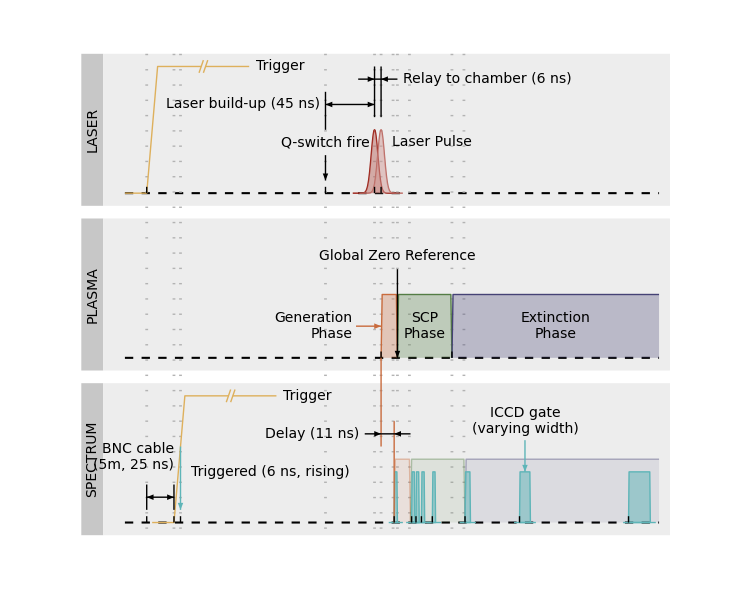

```mathematica
(*--text annotation--*)
opt={FontFamily->"Arial",FontColor->Black,FontSize->14,FontWeight->Plain};

(* -- laser pulse -- *)
a=3/Log[2];
f[t_]:=5Exp[-(t/a)^2];
laser[x_,y_,col_]:={
{col,AbsoluteThickness[1],Line[Table[{x+t,y+f[t]},{t,-20,20,.05}]]},
{EdgeForm[Transparent],FaceForm[{Lighter@col,Opacity[.5]}],Polygon[Table[{x+t,y+f[t]},{t,-20,20,.05}]]}
};

(* -- trigger -- *)
trigger[x_,y_]:={
RGBColor[.87,.69,.36,1],AbsoluteThickness[1],
Line[{{x-20,y},{x,y},{x+10,y+10},{x+50,y+10}}],
Line[{{x+54,y+10},{x+94,y+10}}],
Line[{{x+48,y+10-.5},{x+52,y+10+.5}}],
Line[{{x+52,y+10-.5},{x+56,y+10+.5}}],
Text[Style["Trigger",FontColor->RGBColor[.87,.69,.36,1],opt],{x+100,y+10},{-1,0}]
};

(* -- ICCD gate -- *)
gate[x_,y_,w_]:={
{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1],Line[{{x-5,y},{x+w+5,y}}]},
{EdgeForm[{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1]}],FaceForm[{RGBColor[0.37, 0.71, 0.72, 1],Opacity[.5]}],Polygon[{{x,y},{x+.5,y+4},{x+w-.5,y+4},{x+w,y}}]}
};

(* -- grids & ticks -- *)
grids=Table[
{RGBColor[.7,.7,.7,1],AbsoluteThickness[2],AbsoluteDashing[{1,10}],Line[{{t,11},{t,-27}}]},
{t,{-230,-205,-199,-66,-21,-15,-4,0,11,50,61}}];
ticks[x_List,y_]:=Table[{Black,AbsoluteThickness[1],Line[{{t,y},{t,y+.5}}]},{t,x}];

(* -- plot -- *)
gf=ListLinePlot[

{},

Prolog->{
(* -- laser -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-1},{-270,11}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-1},{250,11}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,0},{240,0}}]},
Text[Style["LASER",FontWeight->Bold,opt],{-280,5},{0,0},{0,1}],

(* -- plasma -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-14},{-270,-2}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-14},{250,-2}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,-13},{240,-13}}]},
Text[Style["PLASMA",FontWeight->Bold,opt],{-280,-8},{0,0},{0,1}],

(* -- Image -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-290,-27},{-270,-15}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-270,-27},{250,-15}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-250,-26},{240,-26}}]},
Text[Style["SPECTRUM",FontWeight->Bold,opt],{-280,-21},{0,0},{0,1}],

(* -- vertical grids -- *)
grids
},

Epilog->{
(* -- laser -- *)
trigger[-230,0],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-66,3},{-66,1}}]},
Text[Style["Q-switch fire",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-66,4},{0,0}],
Text[Style["Laser Pulse",FontColor->RGBColor[0.6, 0.11, 0.07, 1],Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-5,4},{-1,0}],
{Black,Opacity[1],Line[{{-66,5},{-66,8}}]},
{Black,Opacity[1],Line[{{-21,6},{-21,10}}]},
{Black,Opacity[1],Line[{{-15,6},{-15,10}}]},
{Black,Opacity[1],Arrowheads[{-.015,.015}],Arrow[{{-66,7},{-21,7}}]},
Text[Style["Laser build-up (45 ns)",opt],{-71,7},{1,0}],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-36,9},{-21,9}}]},
{Black,Opacity[1],Line[{{-21,9},{-15,9}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{0,9},{-15,9}}]},
Text[Style["Relay to chamber (6 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{5,9},{-1,0}],
laser[-21,0,RGBColor[0.6, 0.11, 0.07, 1]],
laser[-15,0,RGBColor[0.7333333333333333, 0.4066666666666666, 0.37999999999999995, 1]],

(* -- plasma -- *)
{RGBColor[0.79, 0.42, 0.24, 1],AbsoluteThickness[1],Line[{{-15,-13},{-14,-8},{-1,-8},{0,-13}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.3]}],Polygon[{{-15,-13},{-14,-8},{-1,-8},{0,-13}}]},
Text[Style["Generation\nPhase",FontColor->RGBColor[0.79, 0.42, 0.24, 1],Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-41,-10.5},{1,0}],
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{-38,-10.5},{-15,-10.5}}]},
{RGBColor[0.33, 0.49, 0.27, 1],AbsoluteThickness[1],Line[{{0,-13},{1,-8},{49,-8},{50,-13}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.3]}],Polygon[{{0,-13},{1,-8},{49,-8},{50,-13}}]},
Text[Style["SCP\nPhase",FontColor->RGBColor[0.33, 0.49, 0.27, 1],opt],{25,-10.5},{0,0}],
{RGBColor[0.27, 0.26, 0.46, 1],AbsoluteThickness[1],Line[{{50,-13},{51,-8},{240,-8}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.3]}],Polygon[{{50,-13},{51,-8},{240,-8},{240,-13}}]},
Text[Style["Extinction\nPhase",FontColor->RGBColor[0.27, 0.26, 0.46, 1],opt],{145,-10.5},{0,0}],
Text[Style["Global Zero Reference",Background->RGBColor[0.93, 0.93, 0.93, 1],FontWeight->Bold,opt],{0,-5},{0,0}],
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{0,-6},{0,-13}}]},

(* -- Spectrum -- *)
trigger[-205,-26],
{Black,Opacity[1],Line[{{-230,-25},{-230,-23}}]},
{Black,Opacity[1],Line[{{-205,-25},{-205,-23}}]},
{Black,Opacity[1],Arrowheads[{-.015,.015}],Arrow[{{-230,-24},{-205,-24}}]},
Text[Style["BNC cable\n(5m, 25 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],TextAlignment->Left,opt],{-205,-22},{1,-1}],
{RGBColor[0.37, 0.71, 0.72, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{-199,-20},{-199,-25}}]},
{FaceForm[Transparent],EdgeForm[{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[2]}],Disk[{-199,-20},Offset[4]]},
Text[Style["Triggered (6 ns, rising)",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{-189,-22},{-1,0}],
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.4],AbsoluteThickness[1],Line[{{-3,-26},{-2,-21},{11,-21},{12,-26}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.1]}],Polygon[{{-3,-26},{-2,-21},{11,-21},{12,-26}}]},
{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.4],AbsoluteThickness[1],Line[{{12,-26},{13,-21},{61,-21},{62,-26}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.1]}],Polygon[{{12,-26},{13,-21},{61,-21},{62,-26}}]},
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.4],AbsoluteThickness[1],Line[{{62,-26},{63,-21},{240,-21}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.1]}],Polygon[{{62,-26},{63,-21},{240,-21},{240,-26}}]},
MapThread[gate[#1,-26,#2]&,{{-3,13,17,22,32,62,112,212},{3,3,3,3,3,5,10,20}}],
Text[Style["ICCD gate\n(varying width)",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{117,-18},{0,0}],
{RGBColor[0.37, 0.71, 0.72, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{117,-19.5},{117,-22}}]},
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Line[{{-15,-13},{-15,-20}}]},
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Line[{{-3,-26},{-3,-18}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{-30,-19},{-15,-19}}]},
{Black,Opacity[1],Line[{{-15,-19},{-3,-19}}]},
{Black,Opacity[1],Arrowheads[{0,.015}],Arrow[{{12,-19},{-3,-19}}]},
Text[Style["Delay (11 ns)",Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-35,-19},{1,0}],

ticks[{-230,-66,-21,-15},0],
ticks[{-15,0,50},-13],
ticks[{-230,-205,-199,-3,13,17,22,32,62,112,212},-26]

},

Joined->True,
PlotRange->{{-290,250},{-27,11}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->opt,

PlotStyle->{
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]}
},

Axes->False,
Frame->False,
GridLines->None,

ImagePadding->0,
ImageSize->(130*2)*(72/25.4),
AspectRatio->.8

];

Print[gf];

Export[NotebookDirectory[]<>"specSequence.pdf",gf];
```

## ICCD gating

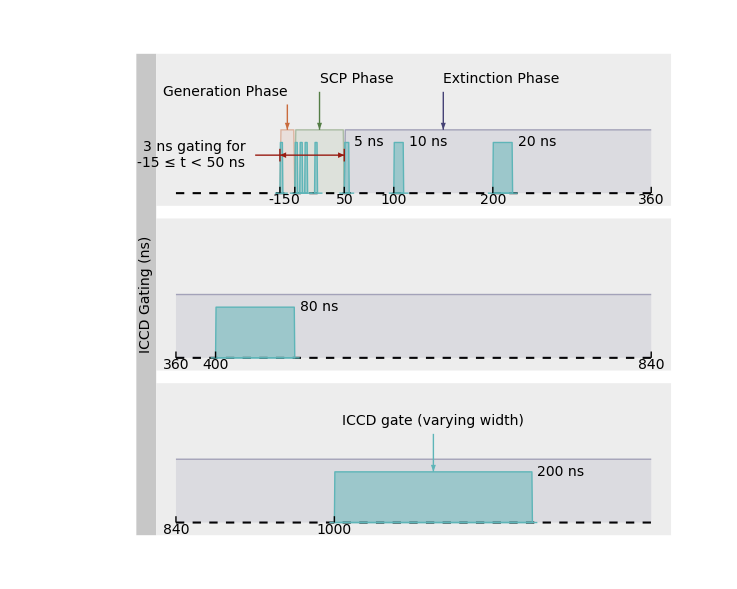

```mathematica
(*--text annotation--*)
opt={FontFamily->"Arial",FontColor->Black,FontSize->14,FontWeight->Plain};

(* -- laser pulse -- *)
a=3/Log[2];
f[t_]:=5Exp[-(t/a)^2];
laser[x_,y_,col_]:={
{col,AbsoluteThickness[1],Line[Table[{x+t,y+f[t]},{t,-20,20,.05}]]},
{EdgeForm[Transparent],FaceForm[{Lighter@col,Opacity[.5]}],Polygon[Table[{x+t,y+f[t]},{t,-20,20,.05}]]}
};

(* -- trigger -- *)
trigger[x_,y_]:={
RGBColor[.87,.69,.36,1],AbsoluteThickness[1],
Line[{{x-20,y},{x,y},{x+10,y+10},{x+50,y+10}}],
Line[{{x+54,y+10},{x+94,y+10}}],
Line[{{x+48,y+10-.5},{x+52,y+10+.5}}],
Line[{{x+52,y+10-.5},{x+56,y+10+.5}}],
Text[Style["Trigger",FontColor->RGBColor[.87,.69,.36,1],opt],{x+100,y+10},{-1,0}]
};

(* -- ICCD gate -- *)
gate[x_,y_,w_]:={
{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1],Line[{{x-5,y},{x+w+5,y}}]},
{EdgeForm[{RGBColor[0.37, 0.71, 0.72, 1],AbsoluteThickness[1]}],FaceForm[{RGBColor[0.37, 0.71, 0.72, 1],Opacity[.5]}],Polygon[{{x,y},{x+.5,y+4},{x+w-.5,y+4},{x+w,y}}]}
};
gateLabel[x_,y_,w_]:={
Text[Style[ToString@w<>" ns",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{x+w+5,y+4},{-1,0}]
};

(* -- grids & ticks -- *)
ticks[x_List,y_]:=Table[{
{Black,AbsoluteThickness[1],Line[{{t,y},{t,y+.5}}]},
Text[Style[Which[y≥-1,t,y≥-14,t+480,y≥-27,t+960],FontSize->12,opt],{t,y},{0,1.2}]
},{t,x}];

(* -- plot -- *)
gf=ListLinePlot[

{},

Prolog->{
(* -- gating -- *)
{RGBColor[0.78, 0.78, 0.78, 1],Rectangle[{-160,-27},{-140,11}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-140,-1},{380,11}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-120,0},{360,0}}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-140,-14},{380,-2}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-120,-13},{360,-13}}]},
{RGBColor[0.93, 0.93, 0.93, 1],Rectangle[{-140,-27},{380,-15}]},
{Black,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[6],Line[{{-120,-26},{360,-26}}]},
Text[Style["ICCD Gating (ns)",FontWeight->Bold,opt],{-150,-8},{0,0},{0,1}]
},

Epilog->{
(* -- line 1 -- *)
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.4],AbsoluteThickness[1],Line[{{-15,0},{-14,5},{-1,5},{0,0}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.79, 0.42, 0.24, 1],Opacity[.1]}],Polygon[{{-15,0},{-14,5},{-1,5},{0,0}}]},
Text[Style["Generation Phase",FontColor->RGBColor[0.79, 0.42, 0.24, 1],Background->RGBColor[0.93, 0.93, 0.93, 1],opt],{-7,8},{1,0}],
{RGBColor[0.79, 0.42, 0.24, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{-7.5,7},{-7.5,5}}]},
{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.4],AbsoluteThickness[1],Line[{{0,0},{1,5},{49,5},{50,0}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.33, 0.49, 0.27, 1],Opacity[.1]}],Polygon[{{0,0},{1,5},{49,5},{50,0}}]},
Text[Style["SCP Phase",FontColor->RGBColor[0.33, 0.49, 0.27, 1],opt],{25,9},{-1,0}],
{RGBColor[0.33, 0.49, 0.27, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{25,8},{25,5}}]},
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.4],AbsoluteThickness[1],Line[{{50,0},{51,5},{360,5}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.1]}],Polygon[{{50,0},{51,5},{360,5},{360,0}}]},
Text[Style["Extinction Phase",FontColor->RGBColor[0.27, 0.26, 0.46, 1],opt],{150,9},{-1,0}],
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{150,8},{150,5}}]},

(* -- line 2 -- *)
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.4],AbsoluteThickness[1],Line[{{-120,-8},{360,-8}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.1]}],Polygon[{{-120,-13},{-120,-8},{360,-8},{360,-13}}]},

(* -- line 3 -- *)
{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.4],AbsoluteThickness[1],Line[{{-120,-21},{360,-21}}]},
{EdgeForm[Transparent],FaceForm[{RGBColor[0.27, 0.26, 0.46, 1],Opacity[.1]}],Polygon[{{-120,-26},{-120,-21},{360,-21},{360,-26}}]},
Text[Style["ICCD gate (varying width)",FontColor->RGBColor[0.37, 0.71, 0.72, 1],opt],{140,-18},{0,0}],
{RGBColor[0.37, 0.71, 0.72, 1],Opacity[1],Arrowheads[{0,.015}],Arrow[{{140,-19},{140,-22}}]},

(* -- gate -- *)
MapThread[gate[#1,0,#2]&,{{-15,0,5,10,20,50,100,200},{3,3,3,3,3,5,10,20}}],
MapThread[gateLabel[#1,0,#2]&,{{50,100,200},{5,10,20}}],
gate[-80,-13,80],
gateLabel[-80,-13,80],
gate[40,-26,200],
gateLabel[40,-26,200],
{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1],Line[{{-15,2.5},{-15,3.5}}]},
{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1],Line[{{50,2.5},{50,3.5}}]},
{RGBColor[0.6, 0.11, 0.07, 1],AbsoluteThickness[1],Line[{{-40,3},{-15,3}}]},
{RGBColor[0.6, 0.11, 0.07, 1],Arrowheads[{-.015,.015}],Arrow[{{-15,3},{50,3}}]},
Text[Style["3 ns gating for\n-15 ≤ t < 50 ns",FontColor->RGBColor[0.6, 0.11, 0.07, 1],opt],{-50,3},{1,0}],

ticks[{-15,0,50,100,200,360},0],
ticks[{-120,-80,360},-13],
ticks[{-120,40},-26]

},

Joined->True,
PlotRange->{{-160,380},{-27,11}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->opt,

PlotStyle->{
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]}
},

Axes->False,
AxesOrigin->{0,0},
AxesStyle->{{Red,AbsoluteThickness[2]},{Red,AbsoluteThickness[2]}},
Frame->False,
GridLines->None,

ImagePadding->0,
ImageSize->(130*2)*(72/25.4),
AspectRatio->.8

];

Print[gf];

Export[NotebookDirectory[]<>"gatingSequence.pdf",gf];
```